## Dengue 7-1-7 analysis — Thailand (2016–2024)

Author: Sompob Saralamba

Affiliation: Mahidol Oxford Tropical Medicine Research Unit (MORU)

Contact: sompob@tropmedres.ac

This notebook reproduces analyses in : "How much could faster outbreak response reduce dengue burden? 
A 7-1-7–inspired analysis using national surveillance data from Thailand."

### Overview

This notebook implements the data cleaning, outbreak detection, counterfactual scenario analyses, and bootstrap uncertainty quantification used in the manuscript . 
Outputs include :

weekly threshold plot used to identify outbreaks (Figure 1)

sensitivity plot of median cases averted vs weeks shortened (Figure 2)

supplementary tables of outbreak - specific counterfactual estimates

```mathematica
(*Record session info*)
$VersionNumber
$OperatingSystem
DateString[]
SeedRandom[12345];
```

14.3

Windows

Tue 24 Feb 2026 10:39:52

### Data Input

The example of the data format.

```mathematica
data=Import["YOURDATA.CSV","Dataset"];
```

```mathematica
q={0.70,0.75,0.80,0.85,0.90};
baselineByWeek=Query[GroupBy[#week&],Median,#cases&][data];
thresholdByWeek=Table[Query[GroupBy[#week&],Quantile[#,j]&,#cases&][data],{j,q}];
```

```mathematica
ab80=Map[Function[r,With[{w=r["week"]},Join[r,<|"baseline"->baselineByWeek[w],"threshold"->thresholdByWeek[[3]][w],"above"->(r["cases"]>thresholdByWeek[[3]][w])|>]]],data];
```

```mathematica
outbreak80=Table[
trsh=Select[Normal@Select[ab80,#year==yr&][All,{#week,#cases,#above}&],#[[3]]==True&][[All,{1,2}]];
trshass=Association[#1->#2&@@@trsh];
runs=Select[Split[trsh[[All,1]],#2==#1+1&],Length[#]>=2&];
intervals={First[#],Last[#]}&/@runs;
lengths=Length/@runs;
Flatten[Thread[{#,Lookup[trshass,#]}]&/@runs,1],
{yr,{2019,2023,2024}}
]
```

```mathematica
Clear[consecutiveIntervals];
consecutiveIntervals[trshlist_,minLen_:2]:=Module[{runs,list,assc,tot,max,t2peak},
assc=(#1->#2&@@@trshlist)//Association;
list=trshlist[[All,1]];
runs=Select[Split[list,#2==#1+1&],Length[#]>=minLen&];
tot=Total/@(Lookup[assc,#]&/@runs);
max=Max/@(Lookup[assc,#]&/@runs);
t2peak=PositionLargest/@(Lookup[assc,#]&/@runs)-1;
<|"Intervals"->({First[#],Last[#]}&/@runs),"Lengths"->(Length/@runs),"total"->tot,"Maximum"->max,"Time2Peak"->t2peak|>]
```

```mathematica
ExtractInfo[Y_Integer]:=Module[{trsh},
trsh=Select[Normal@Select[ab80,#year==Y&][All,{#week,#cases,#above}&],#[[3]]==True&][[All,{1,2}]];
consecutiveIntervals[trsh]
];
```

```mathematica
Dataset@Association@Table[y->ExtractInfo[y],{y,2016,2024}]
```

```mathematica
epi=Import["outbreak_80.csv","Dataset"]
```

```mathematica
ShortenByK[ds_Dataset,k_Integer?NonNegative]:=ds[All,Function[row,Module[{d=row["duration"],tc=row["total_cases"],d2,tc2},d2=Max[1,d-k];
tc2=tc*(d2/d);
(*proportional reduction*)
Join[row,<|"cf_duration"->d2,"cf_total_cases"->tc2,"cases_averted"->(tc-tc2),"pct_averted"->100.0*(tc-tc2)/tc|>]]]];
```

```mathematica
short1=ShortenByK[epi,1]
```

```mathematica
short2=ShortenByK[epi, 2]
```

```mathematica
short3=ShortenByK[epi,3]
```

```mathematica
short4=ShortenByK[epi,4]
```

```mathematica
iqr=N@Normal@Quantile[#[All,#"cases_averted"&],{0.25,0.5,0.75}]&/@{short1,short2,short3,short4}
```

{{1251.,3741.,5607.5},{2502.,5607.5,7610.43},{3753.,6475.2,11415.6},{5004.,8633.6,15220.9}}

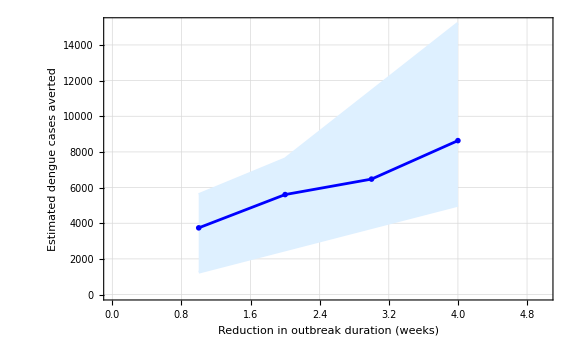

```mathematica
ListPlot[{iqr[[All,2]],iqr[[All,1]],iqr[[All,3]]},Joined->{True,True,True},Frame->True,GridLines->Automatic,PlotRange->{{0,5},{0,Automatic}},PlotMarkers->{"OpenMarkers",None,None},PlotStyle->{Blue,LightBlue,LightBlue},Filling->{2->{3}},FillingStyle->LightBlue,FrameLabel->{"Reduction in outbreak duration (weeks)", "Estimated dengue cases averted"},LabelStyle->Directive[Bold, Medium,FontFamily->"Times New Roman"],ImageSize->Large]
```

```mathematica
targetQ=0.25;
targetDur=Quantile[Normal[epi[All,"duration"]],targetQ];

ShortenToTarget[ds_Dataset,target_Integer?Positive]:=ds[All,Function[row,Module[{d=row["duration"],tc=row["total_cases"],d2,tc2},d2=Min[d,target];(*only shorten,never lengthen*)
tc2=tc*(d2/d);
Join[row,<|"cf_duration"->d2,"cf_total_cases"->tc2,"cases_averted"->(tc-tc2),"pct_averted"->100.0*(tc-tc2)/tc|>]]]];

cfTarget=ShortenToTarget[epi,Round[targetDur]];
cfTarget
```

```mathematica
BootstrapAverted[ds_Dataset,makeCF_,n_Integer:2000]:=Module[{rows=Normal[ds],m=Length[Normal[ds]],totals},totals=Table[Module[{sample,cf},sample=RandomChoice[rows,m];(*resample rows with replacement*)
cf=makeCF[Dataset[sample]];
Total[Normal[cf[All,"cases_averted"]]]],{n}];
<|"mean_averted"->Mean[totals],"median_averted"->Median[totals],"CI95"->Quantile[totals,{0.025,0.975}]|>];
```

```mathematica
(*shorten by 2 weeks*)
BootstrapAverted[epi,(ShortenByK[#,2]&),5000]//N
```

<|mean_averted→42900.,median_averted→42679.9,CI95→{26880.3,61085.8}|>

```mathematica
BootstrapAverted[epi,(ShortenToTarget[#,Round[targetDur]]&),5000]//N
```

<|mean_averted→103406.,median_averted→101326.,CI95→{28833.8,188254.}|>

```mathematica
RandomAchievableCF[ds_Dataset,bestFrac_:0.5]:=Module[{rows=Normal[ds],dAll,pool,target},dAll=Normal[ds[All,"duration"]];
pool=TakeSmallest[dAll,Max[1,Ceiling[bestFrac*Length[dAll]]]];
(*randomly pick an achievable target duration*)
target=RandomChoice[pool];
ShortenToTarget[ds,target]
];
```

```mathematica
SimulateAvertedDistribution[ds_Dataset,bestFrac_:0.5,n_Integer:5000]:=Module[{totals},
totals=Table[Total[Normal[RandomAchievableCF[ds,bestFrac][All,"cases_averted"]]],{n}];
<|"median_averted"->Median[totals],"IQR"->Quantile[totals,{0.25,0.75}],"CI95"->Quantile[totals,{0.025,0.975}]|>
];
```

```mathematica
N@SimulateAvertedDistribution[epi,0.25,5000]  (*“achieve durations like best 50%”*)
```

<|median_averted→121766.,IQR→{103156.,121766.},CI95→{103156.,121766.}|>

```mathematica
BootstrapSamples[ds_Dataset,makeCF_,n_Integer:5000]:=Module[{rows=Normal[ds],m,totals},m=Length[rows];
totals=Table[Module[{sample,cf},sample=RandomChoice[rows,m];
cf=makeCF[Dataset[sample]];
Total[Normal[cf[All,"cases_averted"]]]],{n}];
totals];
```

```mathematica
SeedRandom[123];
bootVals=BootstrapSamples[epi,(ShortenByK[#,2]&),5000];
```

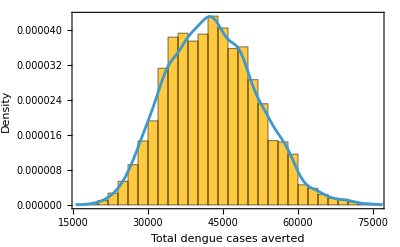

```mathematica
Show[Histogram[bootVals,Automatic,"PDF",Frame->True,FrameLabel->{"Total dengue cases averted","Density"}],
SmoothHistogram[bootVals]]
```